```mathematica
SeedRandom[1];d=Table[{x,Around[10-2x+Round[RandomVariate[NormalDistribution[0,1]],0.1],1]},{x,0,10}]
```

{{0,10.51.0},{1,8.31.0},{2,7.51.0},{3,4.11.0},{4,1.61.0},{5,0.01.0},{6,-2.01.0},{7,-3.91.0},{8,-6.31.0},{9,-7.61.0},{10,-9.31.0}}

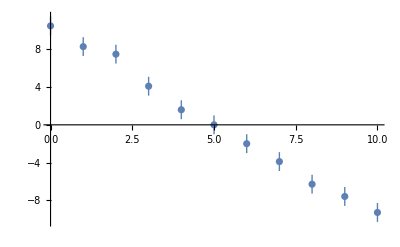

```mathematica
ListPlot[d]
```

```mathematica
linearFit[d_]:=Module[{x,y,sigma,tw1,twX,twXX,twY,twXY,twYY,cInv,c,sigA,sigB,norm,minChiSq,a,b},
x=#[[1]]&/@d;y=#[[2]]["Value"]&/@d;sigma=#[[2]]["Uncertainty"]&/@d;
tw1=Total[1/sigma^2];
twX=Total[x/sigma^2];
twXX=Total[x^2/sigma^2];
twY=Total[y/sigma^2];
twXY=Total[x y/sigma^2];
twYY=Total[ y^2/sigma^2];
cInv={{twXX,twX},{twX,tw1}};
c=Inverse[cInv];
sigA=Sqrt[c[[1,1]]];
sigB=Sqrt[c[[2,2]]];
norm=DiagonalMatrix[{1/sigA,1/sigB}];
minChiSq=twYY-{twXY,twY}.c.{twXY,twY};
{a,b}=c.{twXY,twY};
{x,y,sigma,cInv,{twXY,twY},c,c.{twXY,twY},{sigA,sigB},
norm.c.norm,minChiSq}]
```

```mathematica
fit=linearFit[d]
```

{{0,1,2,3,4,5,6,7,8,9,10},{10.5,8.3,7.5,4.1,1.6,0.,-2.,-3.9,-6.3,-7.6,-9.3},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{{385.,55.},{55.,11.}},{-209.1,2.9},{{0.00909091,-0.0454545},{-0.0454545,0.318182}},{-2.03273,10.4273},{0.0953463,0.564076},{{1.,-0.845154},{-0.845154,1.}},2.62764}

```mathematica
CDF[ChiSquareDistribution[9],fit[[10]]]
```

0.0227484

```mathematica
d1=Table[{x,Around[10-2x+Round[RandomVariate[NormalDistribution[0,1]],0.1],1]},{x,0,10}]
```

{{0,9.41.0},{1,6.71.0},{2,7.71.0},{3,3.51.0},{4,0.81.0},{5,-0.61.0},{6,-3.11.0},{7,-3.91.0},{8,-6.71.0},{9,-5.51.0},{10,-10.61.0}}

```mathematica
fit1=linearFit[d1]
```

14.0428

{{0,1,2,3,4,5,6,7,8,9,10},{9.4,6.7,7.7,3.5,0.8,-0.6,-3.1,-3.9,-6.7,-5.5,-10.6},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{{385.,55.},{55.,11.}},{-222.2,-2.3},{{0.00909091,-0.0454545},{-0.0454545,0.318182}},{-1.91545,9.36818},{0.0953463,0.564076},{{1.,-0.845154},{-0.845154,1.}},14.0428}

```mathematica
CDF[ChiSquareDistribution[9],fit1[[10]]]
```

0.0864231

```mathematica
{a,b}=fit[[7]]
```

{-2.03273,10.4273}

```mathematica
x0=-b/a
```

5.1297

```mathematica
Sqrt[{b/a^2,-1/a}.fit[[6]].{b/a^2,-1/a}]
```

0.148453

```mathematica
TeXForm[Grid[Join[{{"x","y",Style["σ",Bold]}},Transpose[Take[fit,3]]],Frame->All]]
```

\begin{array}{ccc}
 \text{x} & \text{y} & \sigma 
   \\
 0 & 10.5 & 1. \\
 1 & 8.3 & 1. \\
 2 & 7.5 & 1. \\
 3 & 4.1 & 1. \\
 4 & 1.6 & 1. \\
 5 & 0. & 1. \\
 6 & -2. & 1. \\
 7 & -3.9 & 1. \\
 8 & -6.3 & 1. \\
 9 & -7.6 & 1. \\
 10 & -9.3 & 1. \\
\end{array}

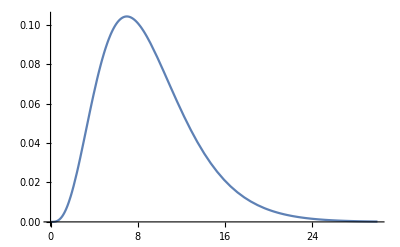

```mathematica
Plot[PDF[ChiSquareDistribution[9],x],{x,0,30}]
```

```mathematica
chiSq[fit_,a_,b_]:=Module[{x,y,sigma},
x=fit[[1]]; y=fit[[2]];sigma=fit[[3]];
Total[(a x + b-y)^2/sigma^2]]
```

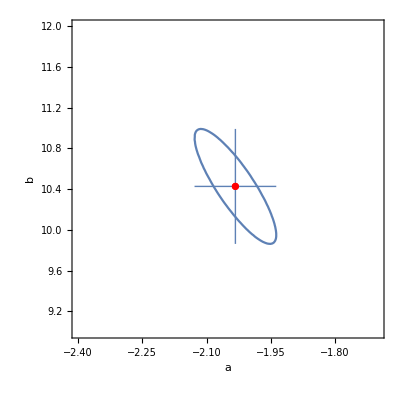

```mathematica
Show[ContourPlot[chiSq[fit,a,b]-fit[[10]]==1,{a,-2.4,-1.7},{b,9,12},Contours->{1},FrameLabel->Automatic],ListPlot[{{Around[fit[[7,1]],fit[[8,1]]],Around[fit[[7,2]],fit[[8,2]]]}},PlotStyle->Red]]
```

```mathematica
cov=fit[[6]];MatrixForm[cov]
```

(0.00909091 | -0.0454545
-0.0454545 | 0.318182)

```mathematica
vecs=Eigenvectors[cov]
```

{{-0.142539,0.989789},{-0.989789,-0.142539}}

```mathematica
esys=Eigensystem[cov]
```

{{0.324728,0.00254504},{{-0.142539,0.989789},{-0.989789,-0.142539}}}

```mathematica
Norm[vecs[[1]]]
```

1.

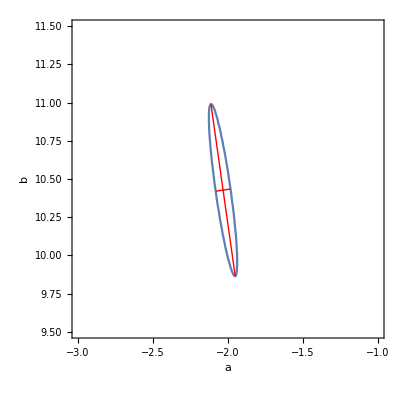

```mathematica
Show[ContourPlot[chiSq[fit,a,b]-fit[[10]]==1,{a,-3,-1},{b,9.5,11.5},Contours->{1},FrameLabel->Automatic],
Graphics[{Red,Line[{{a,b}+Sqrt[esys[[1,1]]]esys[[2,1]],{a,b}-Sqrt[esys[[1,1]]]esys[[2,1]]}],Line[{{a,b}+Sqrt[esys[[1,2]]]esys[[2,2]],{a,b}-Sqrt[esys[[1,2]]]esys[[2,2]]}]}]]
```

```mathematica
?Line
```